## Matrices

```mathematica
Clear[eq,Λ1byτ,Λ2byτ,lhs1,lhs2,rhs1,rhs2,λ1,a1,h1,λ2,a2,h2,eqn1,eqn2,eqn3,eqn4];
G[χ_, η_]=1+χ η ct ctp;
Λ1byτ=-h1+λ1+a1 ct(* Cos[θ] *);
Λ2byτ=-h2+λ2+a2 ct;

lhs1=λ1+a1 ct;
lhs2=λ2+a2 ct;    
rhs1=1/2 βintra intθpf1(-h1+λ1+a1 ctp)G[1,1];
rhs2=1/2 βintra intθpf2(-h2+λ2+a2 ctp)G[-1,-1];

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eq==eqn1+eqn2 ct//FullSimplify

eq=lhs2-rhs2;
eqn3=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eq==eqn3+eqn4 ct//FullSimplify
```

True

True

```mathematica
Clear[arr,array,cmat1,cmat2];arr=CoefficientArrays[{eqn1==0,eqn2==0},{λ1,a1}];
array=(Normal[arr]//FullSimplify)/.ctp->ct;
cmat1=array[[1]]//Expand;cmat2=array[[2]];
rep1={ct h1 intθpf1->hct1,ct h2 intθpf2->hct2,h1 intθpf1->hzero1,h2 intθpf2->hzero2,ct^2 intθpf1->ctct1,ct^2 intθpf2->ctct2,ct intθpf1->ct1,ct intθpf2->ct2,intθpf1->zero1,intθpf2->zero2};
MatrixForm[cmat1/.rep1]//FullSimplify
MatrixForm[cmat2/.rep1]//FullSimplify
```

((hzero1 βintra)/2
(hct1 βintra)/2)

(1-(zero1 βintra)/2 | -(ct1 βintra)/2
-(ct1 βintra)/2 | 1-(ctct1 βintra)/2)

## prel

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,c,v0,ϕ,θp,ϕp,kf,μeff,μ,s} ∈ Reals && k>0 && kf>0 && 0<=θ<=π && 0<=θp<=π && c>0 && v0>0 && μ>0;
repl={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
srep={kf->kf1[θ],(s v0)/(√(kf1[θ]^2))->(s v0)/kf1[θ]};
```

## Fermi surfaces

```mathematica
Solve[k ( c k+s v0)==μ,k]/.s^2->1
```

{{k→(-s v0-√(v0^2+4 c μ))/(2 c)},{k→(-s v0+√(v0^2+4 c μ))/(2 c)}}

```mathematica
(Flatten[Simplify[SolveValues[c k^2+s v0 k +om(B e v0 Cos[θ])/(2 k)==μeff,k],ass]/.{s^3->s,s^2->1},1][[1]])/.μeff->μ-s B mbohr
```

-(s v0)/(3 c)+(2 2^(1/3) (v0^2+3 c (-B mbohr s+μ)))/(3 c (-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3))+1/(6 2^(1/3) c)(-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3)

```mathematica
Clear[kF,B,c,ifun,v];


kF[B_,μ_,c_,v0_,s_,mbohr_,θ_,om_]:=Block[{e=1},

-(s v0)/(3 c)+(2 2^(1/3) (v0^2+3 c (-B mbohr s+μ)))/(3 c (-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3))+1/(6 2^(1/3) c)(-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3)
];

(*ifun[B_,μ_,c_,v0_,s_,mbohr_,om_]:=Block[{e=1,θ,kfvals,dat,len,i,list,div=50},
kfvals[θ_]=-(s v0)/(3 c)+(2 2^(1/3) (v0^2+3 c (-B mbohr s+μ)))/(3 c (-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3))+1/(6 2^(1/3) c)(-16 s v0^3-72 c s v0 (-B mbohr s+μ)-108 B c^2 e om v0 Cos[θ]+4 √(-16 (v0^2+3 c (-B mbohr s+μ))^3+(4 s v0^3+18 c s v0 (-B mbohr s+μ)+27 B c^2 e om v0 Cos[θ])^2))^(1/3);
dat=Table[{θ,kfvals[θ]},{θ,0,π,π/div}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/div,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];*)
```

146.524

146.524

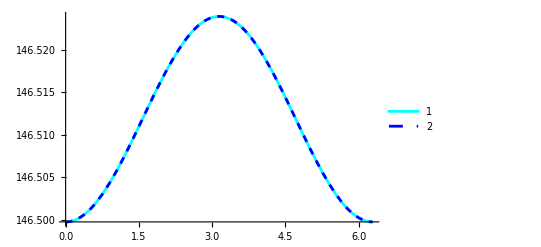

1

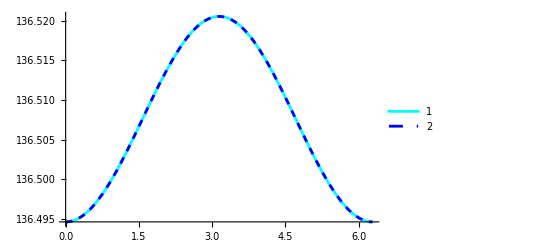

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;sval=-1;bval=100;
ifun[bval,mu,cval,v0val,sval,bohrrm,omval][π]//Chop
kF[bval,mu,cval,v0val,sval,bohrrm,π,omval]//Chop
Plot[{kF[bval,mu,cval,v0val,sval,bohrrm,θ,omval],ifun[bval,mu,cval,v0val,sval,bohrrm,omval][θ]},{θ,0,2π},PlotStyle->{Cyan,Directive[Dashed,Blue]},PlotRange->All,PlotLegends->Automatic]
sval=1
Plot[{kF[bval,mu,cval,v0val,sval,bohrrm,θ,omval],ifun[bval,mu,cval,v0val,sval,bohrrm,omval][θ]},{θ,0,2π},PlotStyle->{Cyan,Directive[Dashed,Blue]},PlotRange->All,PlotLegends->Automatic]
```

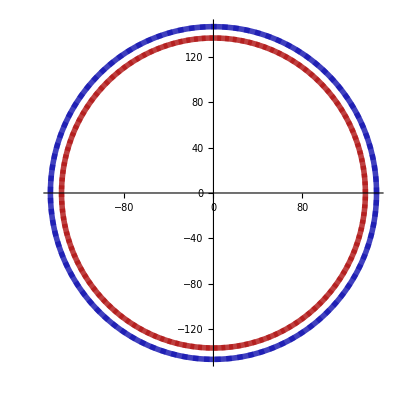
{-Graphics-,-Graphics-}

```mathematica
mu=10.0^-0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=0 3*10^-7 ;bval=100;
rot=-π/2;
thk=0.01;style={Directive[Darker[Red],Thickness[thk],Dashing[0.007],Opacity[0.5]],Directive[Darker[Blue],Thickness[thk],Dashing[0.01],Opacity[0.5]],(**)Directive[Darker[Red],Thickness[thk],Opacity[0.75]],Directive[Darker[Blue],Thickness[thk],Opacity[0.75]]};
sval=1;

PolarPlot[{(√(v0val^2+4 cval mu)-v0val)/(2 cval),(√(v0val^2+4 cval mu)+v0val)/(2 cval),kF[bval,mu,cval,v0val,1,bohrrm,θ+rot,omval],kF[bval,mu,cval,v0val,-1,bohrrm,θ+rot,omval]},{θ,0,2π},PlotStyle->style];
sval=-1;
PolarPlot[{(√(v0val^2+4 cval mu)-v0val)/(2 cval),(√(v0val^2+4 cval mu)+v0val)/(2 cval),kF[bval,mu,cval,v0val,1,bohrrm,θ+rot,omval],kF[bval,mu,cval,v0val,-1,bohrrm,θ+rot,omval]},{θ,0,2π},PlotStyle->style];
{p1,p2}
```

## phys qty

```mathematica
Print["zeroth band vel, vvec:"]
vvec = FullSimplify[Grad[ c  (kx^2+ky^2+kz^2)+s v0 √(kx^2+ky^2+kz^2),{kx,ky,kz}],ass];
vvec=FullSimplify[FullSimplify[vvec/.repl,ass]/.srep]
Clear[s,mvec,Bvec,kf,dotprod];
mvec=(-e v0 { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) (* -Graphics-*);
Bvec=B{0,0,1};
Print["BC vector:"](* -Graphics- *);
Ωvec=-s/(2(kf1[θ])^3)FullSimplify[{kx,ky,kz}/.repl,Assumptions->ass]/.srep
Print["omm energy:"];
 dotprod=-mvec.Bvec;
FullSimplify[dotprod/.repl,ass]/.srep
Print["omm velocity:"];
 vomm=om FullSimplify[Grad[dotprod,{kx,ky,kz}]/.repl,ass]/.srep

Print["tot vel. velocity, z-xomp"];
vtot=(vomm+vvec)//FullSimplify;
vtot[[3]]

Print["vtot.k:"];
FullSimplify[kf1[θ]FullSimplify[vtot.{ Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}]//TrigExpand]
Print["Ω.vtot:"];
FullSimplify[Expand[vtot.Ωvec]/.s^2->1]
```

zeroth band vel, vvec:

{Cos[ϕ] (s v0+2 c kf1[θ]) Sin[θ],(s v0+2 c kf1[θ]) Sin[θ] Sin[ϕ],Cos[θ] (s v0+2 c kf1[θ])}

BC vector:

{-(s Cos[ϕ] Sin[θ])/(2 kf1[θ]^2),-(s Sin[θ] Sin[ϕ])/(2 kf1[θ]^2),-(s Cos[θ])/(2 kf1[θ]^2)}

omm energy:

(B e v0 Cos[θ])/(2 kf1[θ])

omm velocity:

{-(B e om v0 Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B e om v0 Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B e om v0 Cos[2 θ])/(2 kf1[θ]^2)}

tot vel. velocity, z-xomp

s v0 Cos[θ]-(B e om v0 Cos[2 θ])/(2 kf1[θ]^2)+2 c Cos[θ] kf1[θ]

vtot.k:

-(B e om v0 Cos[θ])/(2 kf1[θ])+s v0 kf1[θ]+2 c kf1[θ]^2

Ω.vtot:

(B e om s v0 Cos[θ]-2 kf1[θ]^2 (v0+2 c s kf1[θ]))/(4 kf1[θ]^4)

## sigma trials

```mathematica
Clear[sig,s,c,μ,B,v0];
sig[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]:=Block[{e=1,βinter =0,kf1vec,kf2vec,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,cs,λ1,λ2,a1,a2,cost,θp,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},

kf1[θ_]=kF[B,μ,c,v0,s,mbohr,θ,χ];
kf1vec[θ_]=kf1[θ]{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
bc1[θ_]=(-s χ)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(- χ B e v0)/(2 kf1[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=-(B e χ v0 Cos[θ])/(2 kf1[θ])+s v0 kf1[θ]+2 c kf1[θ]^2;
h1[θ_]=1/Dphase1[θ](s v0 Cos[θ]-(B e χ v0 Cos[2 θ])/(2 kf1[θ]^2)+2 c Cos[θ] kf1[θ]+e B χ((B e χ s v0 Cos[θ]-2 kf1[θ]^2 (v0+2 c s kf1[θ]))/(4 kf1[θ]^4)));
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero1 βintra)}, {1/2 (hct1 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
cs=λ1 zero1-hzero1+a1 ct1;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]);
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
{B,mat,colvec,{zero1, hzero1,ct1}}
];
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;sval=-1;bval=1;
Quiet[sig[bval,mu,cval,v0val,1,bohrrm,omval,1]]//Chop
```

{1,{{0,5.96997×10^-6},{5.96997×10^-6,0.666667}},{-3.3745×10^-7,0.00471699},{2.,-6.74899×10^-7,-0.0000119399}}

```mathematica
Clear[sigt,s,c,μ,B,v0];
sigt[B_,μ_,c_,v0_,βintra_,mbohr_]:=Block[{e=1,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,λ11,a11,λ21,a21,sig11,sig21,sig12,sig22,mat1,mat2,c1,c2,mt,mat,ct,cs1,cs2,sol,mat11,mat12,mat22,mat21,c11,c21,c22,c12},
(* sig[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] gives {B,mat,colvec,{zero1, hzero1,ct1}} *)
sig11=sig[B,μ,c,v0,βintra,mbohr,1,1];
sig12=sig[B,μ,c,v0,βintra,mbohr,1,-1];

sig21=sig[B,μ,c,v0,βintra,mbohr,-1,1];
sig22=sig[B,μ,c,v0,βintra,mbohr,-1,-1];

mat11=sig11[[2]]; mat12=sig12[[2]];mat22=sig22[[2]]; mat21=sig21[[2]];
c11=sig11[[3]]; c21=sig21[[3]];c21=sig21[[3]]; c22=sig22[[3]];

mt=ArrayFlatten[{{mat11,0},{0,mat21}}];
ct=Join[c11,c21];(* cs=λ1 zero1-hzero1+a1 ct1; *)
cs1=λ11 sig11[[4,1]]-sig11[[4,2]]+a11 sig11[[4,3]];
cs2=λ21 sig21[[4,1]]-sig21[[4,2]]+a21 sig21[[4,3]];
mat=mt.{λ11,a11,λ21,a21};

sol=Flatten[Solve[{mat[[1]]+ct[[1]]==0,mat[[3]]+ct[[3]]==0,cs1==0,cs2==0},{λ11,a11,λ21,a21}],1];
Print[MatrixForm[mat],"\t",MatrixForm[ct],"\t",cs1,"\t",cs2,"\t",Chop[cs1+cs2]];
{MatrixRank[mt],sol}
];

mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; bohrrm= 3*10^-7  0;bval=100;vin=1;
Quiet[sigt[bval,mu,cval,v0val,vin,bohrrm]]//Chop
```

(0.0601495 a11+0.00539717 λ11
0.670344 a11+0.0601495 λ11
-0.0601495 a21+0.00539717 λ21
0.670344 a21-0.0601495 λ21)	(-0.00338764
0.00462992
0.00338764
0.00462992)	0.00677528-0.120299 a11+1.98921 λ11	-0.00677528+0.120299 a21+1.98921 λ21	-0.120299 a11+0.120299 a21+1.98921 λ11+1.98921 λ21

{2,{λ11→0,a11→0.0563204,λ21→0,a21→0.0563204}}

```mathematica
Solve[{0.007031581205519263 a11+0.00007415786607711805 λ11==-0.00012481802801792593,0.00024963605603585187-0.014063162411038527 a11+1.9998516842678458 λ11==0},{a11,λ11}]
```

{{a11→-0.0177484,λ11→-0.000249636}}

## sig final: use only one eqn from the rank-1 matrix

```mathematica
Clear[sign,s,c,μ,B,v0];
sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]:=Block[{e=1,βinter =0,cond,matr,bc1,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vmm1,vdotk1,vdotk2,cs,λ1,a1,cost,θp,Dphase1,Dphase2,h1,vz1,zero1,ct1,ctct1,hzero1,hct1,hstcp1,hstsp1,colvec,mat,sol,sol1,Λ1,s1,int1},

kf1[θ_]=kF[B,μ,c,v0,s,mbohr,θ,χ];
bc1[θ_]=(-s χ)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(- χ B e v0)/(2 kf1[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=s v0 kf1[θ]+2 c kf1[θ]^2-(B e χ v0 Cos[θ])/(2 kf1[θ]);
h1[θ_]=1/Dphase1[θ]( (vvec1[θ]+vmm1[θ])[[3]]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 hzero1 βintra}, {1/2 hct1 βintra}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol=Flatten[Solve[{matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
(* choosing wrong matrix elements above give wrong solns; choice can be fixed by the answer from sig0 below *)
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ],{θ,0,π}];
{B,cond}
];
(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] *)
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=-1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_]*)
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-35,35,10}]
,(*****)Epilog->{Style[Text["No OMM",{0,-1.5}],Blue,16,Bold]}
```

## sigma at B=0

```mathematica
Clear[sig0,s,c,μ,B,v0];
sig0[μ_,c_,v0_,βintra_,s_]:=Block[{e=1,B=0,βinter =0,cond,matr,θ,τ1,τ2,kf1,ϕ=0,f1,vvec1,vdotk1,cs,λ1,λ2,a1,a2,cost,θp,Dphase1,h1,vz1,h2,vz2,zero1,zero2,ct1,ctct1,hzero1,hct1,hct2,hstcp1,hstsp1,colvec,mat,sol,sol1,Λ1,s1,int1},

kf1[θ_]=(√(v0^2+4 c μ)-s v0)/(2 c);
Dphase1[θ_]=1;
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vdotk1[θ_]=2 c kf1[θ]^2+s v0 kf1[θ];
h1[θ_]=1/Dphase1[θ](2 c kf1[θ]+s v0 )Cos[θ];
(*****************)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero1 βintra)}, {1/2 (hct1 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2}});
matr=mat.{λ1,a1};
cs=λ1 zero1-hzero1+a1 ct1;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,cs==0},{λ1,a1}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
cond=NIntegrate[int1[θ],{θ,0,π}];
{0,cond}
];
(* sig0[μ_,c_,v0_,βintra_,s_] *)
mu=10.0^-0; cval=5 10^-5 ;v0val= 5 10^-4;sval=-1;
Quiet[sig0[mu,cval,v0val,1,sval]]//Chop
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4;
Quiet[sig0[mu,cval,v0val,1,sval]]//Chop
```

{0,0.00020025}

{0,0.00020025}

## Results

### spin mag mom part set to zero -> B linear vanishes

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=0 ;
sval=1;
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-65,65,10}]
sig0[mu,cval,v0val,1,sval]
```

{{-65,0.000200249},{-55,0.000200249},{-45,0.00020025},{-35,0.00020025},{-25,0.00020025},{-15,0.00020025},{-5,0.00020025},{5,0.00020025},{15,0.00020025},{25,0.00020025},{35,0.00020025},{45,0.00020025},{55,0.000200249},{65,0.000200249}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {2.32547}. NIntegrate obtained -7.27596×10^-11 and 1.70285×10^-10 for the integral and error estimates.

{0,0.00020025}

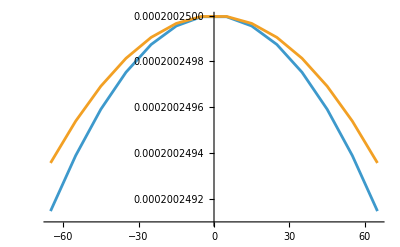

```mathematica
dat1={{-65,0.0002002491457781938},{-55,0.00020024938839735394},{-45,0.00020024959058001865},{-35,0.00020024975232617073},{-25,0.00020024987363579728},{-15,0.00020024995450888654},{-5,0.000200249994945433},{5,0.00020024999494543295},{15,0.00020024995450888645},{25,0.00020024987363579739},{35,0.0002002497523261707},{45,0.00020024959058001865},{55,0.00020024938839735405},{65,0.00020024914577819388}};

dat2={{-65,0.00020024935613934967},{-55,0.0002002495390109452},{-45,0.00020024969140398327},{-35,0.00020024981331844097},{-25,0.00020024990475430072},{-15,0.00020024996571154713},{-5,0.00020024999619017294},{5,0.00020024999619017294},{15,0.00020024996571154724},{25,0.0002002499047543006},{35,0.00020024981331844097},{45,0.0002002496914039833},{55,0.00020024953901094525},{65,0.0002002493561393497}};
ListLinePlot[{dat1,dat2}]
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=0 ;
sval=1;
dat1=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-65,65,10}]
sval=-1;
dat2=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-65,65,10}]
```

{{-65,0.0000202381},{-55,0.0000202415},{-45,0.0000202443},{-35,0.0000202466},{-25,0.0000202482},{-15,0.0000202494},{-5,0.0000202499},{5,0.0000202499},{15,0.0000202494},{25,0.0000202482},{35,0.0000202466},{45,0.0000202443},{55,0.0000202415},{65,0.0000202381}}

```mathematica
sval=-1;
dat2=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-65,65,10}]
```

{{-65,0.0000202451},{-55,0.0000202465},{-45,0.0000202477},{-35,0.0000202486},{-25,0.0000202493},{-15,0.0000202497},{-5,0.00002025},{5,0.00002025},{15,0.0000202497},{25,0.0000202493},{35,0.0000202486},{45,0.0000202477},{55,0.0000202465},{65,0.0000202451}}

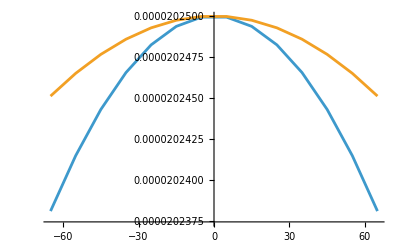

```mathematica
ListLinePlot[{dat1,dat2}]
```

### data for plots

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=-1;(* sign[B_,μ_,c_,v0_,βintra_,mbohr_,χ_,s_] *)
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-65,65,10}]
sig0[mu,cval,v0val,1,sval]
```

{{-65,0.000200245},{-55,0.000200246},{-45,0.000200247},{-35,0.000200248},{-25,0.000200248},{-15,0.000200249},{-5,0.00020025},{5,0.00020025},{15,0.000200251},{25,0.000200251},{35,0.000200252},{45,0.000200252},{55,0.000200253},{65,0.000200253}}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {0.0000120929}. NIntegrate obtained 5.8435×10^-11 and 4.55299×10^-10 for the integral and error estimates.

{0,0.00020025}

```mathematica
list={{-65,0.00020025304579607864},{-55,0.0002002526884081947},{-45,0.00020025229058596002},{-35,0.00020025185232896511},{-25,0.0002002513736368274},{-15,0.00020025085450911143},{-5,0.000200250294945444},{0,0.00020024999999999996},{5,0.0002002496949454192},{15,0.0002002490545086624},{25,0.00020024837363477466},{35,0.0002002476523233774},{45,0.00020024689057408172},{55,0.00020024608838651442},{65,0.00020024524576031953}};
len=Length[list];
x=1/0.00020024999999999996;
dat11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
list={{-65,0.000200245456127652},{-55,0.00020024623900384873},{-45,0.0002002469914000961},{-35,0.00020024771331661207},{-25,0.00020024840475362974},{-15,0.0002002490657113993},{-5,0.00020024969619016254},{0,0.00020025},{5,0.0002002502961901809},{15,0.0002002508657116962},{25,0.00020025140475497837},{35,0.00020025191332027052},{45,0.0002002523914078746},{55,0.00020025283901804348},{65,0.00020025325615105724}};
len=Length[list];
x=1/0.00020025;
dat12=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
ListLinePlot[{dat11,dat12}];
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=-1;
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-105,105,10}]
sig0[mu,cval,v0val,1,sval]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {0.0000120929}. NIntegrate obtained 1.55183×10^-11 and 1.65982×10^-10 for the integral and error estimates.

{0,0.00002025}

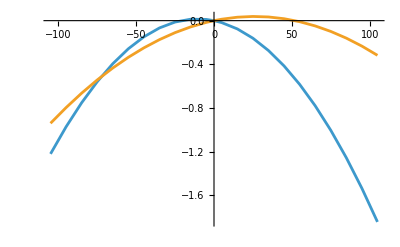

```mathematica
list={{-105,0.00002022528330478294},{-95,0.00002023030913594413},{-85,0.000020234772603487205},{-75,0.000020238673664625702},{-65,0.00002024201227431729},{-55,0.00002024478838525407},{-45,0.000020247001947862872},{-35,0.000020248652910287562},{-25,0.000020249741218388654},{-15,0.00002025026681573588},{-5,0.000020250229643602868},{0,0.000020249999999999994},{5,0.00002024962964096439},{15,0.00002024846674449112},{25,0.000020246740888552483},{35,0.000020244451345307257},{45,0.000020241600024214157},{55,0.0000202381848730218},{65,0.000020234206476777058},{75,0.000020229664758323534},{85,0.000020224559638209738},{95,0.00002021889103468905},{105,0.000020212658863727982}};
len=Length[list];
x=1/0.000020249999999999994;
dat21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
list={{-105,0.00002023096041239716},{-95,0.000020233871400892857},{-85,0.000020236551328945253},{-75,0.000020239000177347856},{-65,0.000020241217930905633},{-55,0.000020243204578431177},{-45,0.000020244960112746954},{-35,0.00002024648277589006},{-25,0.00002024777783305723},{-15,0.00002024884002471163},{-5,0.000020249671114475487},{0,0.000020250000000000004},{5,0.000020250271115176378},{15,0.000020250640043641457},{25,0.000020250777920691098},{35,0.00002025068477113936},{45,0.000020250360623791677},{55,0.000020249805511442648},{65,0.000020249019470877403},{75,0.000020248002542863828},{85,0.000020246754772159122},{95,0.000020245276207502274},{105,0.000020243566901611736}};
len=Length[list];
x=1/0.000020250000000000004;
dat22=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
ListLinePlot[{dat21,dat22}]
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;
sval=1;
dat=Table[Quiet[sign[B,mu,cval,v0val,1,bohrrm,omval,sval]]//Chop,{B,-105,105,10}]
sig0[mu,cval,v0val,1,sval]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {3.1415805607065542416335380757064221768359857378527522087097167969}. NIntegrate obtained -1.42109×10^-12 and 3.91236×10^-12 for the integral and error estimates.

{0,0.00020025}

```mathematica
list={{-105,0.00017821126585871002},{-95,0.0001821859828675223},{-85,0.00018577380325101353},{-75,0.00018897099637009984},{-65,0.0001917743670664769},{-55,0.0001941812079511716},{-45,0.0001961892599173975},{-35,0.00019779667988515298},{-25,0.00019900201499780713},{-15,0.00019980418266753706},{-5,0.00020020245601620154},{0,0.00020025},{5,0.00020019645438824036},{15,0.00019978613872884875},{25,0.00019897181172848268},{35,0.0001977541227392179},{45,0.000196134077572147},{55,0.00019411305339456632},{65,0.00019169281906219373},{75,0.0001888755613547075},{85,0.00018566391773382023},{95,0.00018206101642330045},{105,0.00017807052482791478}};
len=Length[list];
x=1/0.00020024999999999996;
dat31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
list={{-105,0.00018361402643541855},{-95,0.00018659187162412797},{-85,0.000189285771604864},{-75,0.00019169147436963978},{-65,0.00019380523728816125},{-55,0.00019562381460685234},{-45,0.00019714444683860375},{-35,0.00019836485189342684},{-25,0.00019928321782803582},{-15,0.0001998981971170023},{-5,0.00020020890236923782},{0,0.00020024999999999996},{5,0.00020021490343483935},{15,0.00019991622586507503},{25,0.0001993133507070275},{35,0.00019840721563137197},{45,0.00019719921740962997},{55,0.0001956912157748456},{65,0.00019388553871842187},{75,0.0001917849892956116},{85,0.0001893928540339978},{95,0.0001867129130631353},{105,0.0001837494521103172}};
len=Length[list];
x=1/0.00020024999999999996;
dat32=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10},{i,1,len}];
ListLinePlot[{dat31,dat32}];
```

## Plots

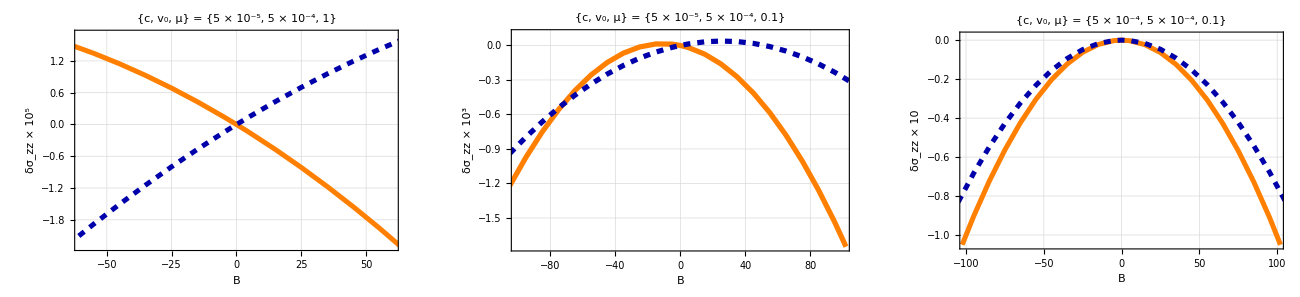

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashed]};

g1=ListPlot[{dat11,dat12},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-60,60},{-2.3,1.7}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^5"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic];
(*************************)

g2=ListLinePlot[{dat21,dat22},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-1.75,0.1}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^3"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->470,GridLines->Automatic];
(*************************)

g3=ListLinePlot[{dat31,dat32},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-1.05,0.02}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{c, v_0, μ} = {5 × 10^-4,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic];


leg=LineLegend[style,{"1","-1"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2,g3}},Spacings->{20,0},ImageSize->1300],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["sepwithomm.pdf",Rasterize[pl],ImageResolution->1000];
```